# Teaching and learning with smart phone and Mathematica

Roger Yu

Mentor: Paul Abbott

## Introduction

Mathematical literacy has become a familiar term in higher education and computational thinking as a way of communicating has also propelled its way into the main stream of our society. As a professional in the area of higher education, I am obligated to make a pathway for our students in all areas of studies to immerse themselves into this technological shift.

This project aims at combining the usages of smart phones and Wolfram Language in the delivery of one of our core courses. The core course  considered here is required for all freshmen students. Approximately 30 sections of the course is offered in each semester and each section has about 30 students coming from all  disciplines ranging from engineering, sciences, math, to arts, and architecture.

Currently, we are already using smart phones as a tool, in some cases the only tool, in hands-on activities or experiments. This project integrates Mathematica with the application of smart phones so to encourage students to make comparisons between theory and observation.

Stephen might prefer Wolfram Language to, or in addition to, talking about Mathematica. Moreover, if you are going to be running primarily on smart phones then maybe you are talking about the Wolfram Cloud App. Alternatively, if the students are downloading captured data to their computer and analyzing there then they would be using the desktop app.

## Integration of smart phones and Mathematica

In the following, we will discuss a few examples of engaging practices that each student will work on his/her own. All of these examples can be chosen by courses at different levels or disciplines.

### Example 1: Voice recognition and analysis

You need to comment on each of these inputs and explain what they do. I have added some comments for this section. You need to add or modify these for the next section.

Also, fuller descriptive names is a better idea.

AudioCapture creates a temporary interactive interface for capturing an audio signal:

```mathematica
audio=AudioCapture[]
```

Spectrogram plots the spectrogram of the captured audio signal:

```mathematica
Spectrogram[audio]
```

-Graphics-

AudioPlot plots the waveform of of the captured audio signal:

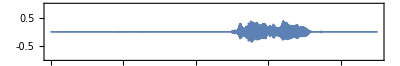

```mathematica
AudioPlot[audio]
```

AudioLocalMeasurements displays the frequencies of the formants of the signal:

```mathematica
timeseries=AudioLocalMeasurements[audio,"Formants"]
```

TimeSeries[…]

Display the frequency time series using ListPlot:

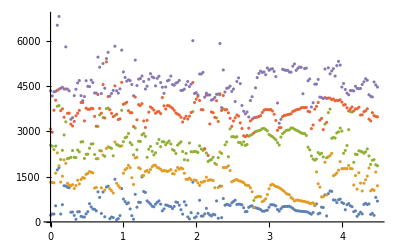

```mathematica
ListPlot[timeseries]
```

Alternatively, use ListLinePlot:

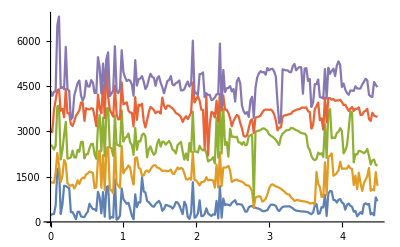

```mathematica
ListLinePlot[timeseries]
```

Use AudioLocalMeasurements to compute the maximum values of the average channel values:

```mathematica
max=AudioLocalMeasurements[audio, "Max"]
```

TimeSeries[…]

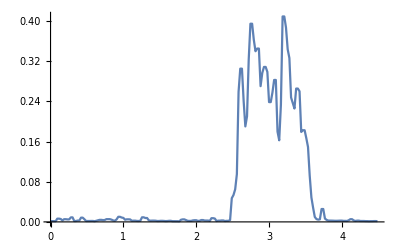

```mathematica
ListLinePlot[max]
```

### Example 2: Analysis of an MP3 audio file

```mathematica
car=Audio[File["ExampleData/car.Mp3"]]
```

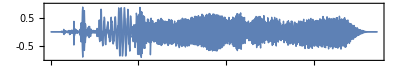

```mathematica
AudioPlot[car]
```

```mathematica
maxcar=AudioLocalMeasurements[car,"Max"]
```

TimeSeries[…]

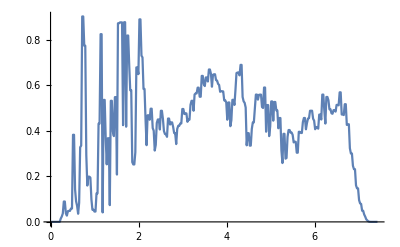

```mathematica
ListLinePlot[maxcar]
```

### Example 3: Analysis of audio signals captured by smart phone

It is dangerous to use a local file. Better approaches are to use DataDrop or  Iconize the imported data.

Rename these inputs to something more descriptive

```mathematica
aaa=Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/Recording 2019-07-04 09-22-43.wav"]
```

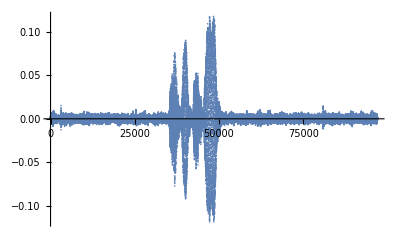

```mathematica
ListPlot[AudioData[aaa],PlotRange->All]
```

```mathematica
Manipulate[
Periodogram[aaa,width], {width,100, 8000,1},SaveDefinitions->True]
```

### Example 4: Analysis of audio signals from an air tube

```mathematica
Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/IMG_3601.jpg"]
```

-Graphics-

Add a comment and link to the following demonstration:

A nice example is the demonstration Resonance in Open and Closed Pipes.

Give a figure  caption. I have cropped the figure

```mathematica
Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/IMG_3602-1.jpg"]
```

-Graphics-

It would be better to do a screen snapshot: press and hold the Side button on the right side of your iPhone. Immediately click the Volume up button on the left side, then release the buttons. A thumbnail of your screenshot appears in the lower-left corner of your iPhone and the photo will be saved to your Photos. Share or export the photo and then import it

```mathematica
Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/IMG_3603.jpg"]
```

-Graphics-

This needs to be imported and then animated using ListAnimate.

```mathematica
video=Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/IMG_3606.TRIM.MOV","ImageList"];
```

### At this point, I don’t have a tube to work with so I can only discuss the example using photos and videos as shown above.